# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Lecture 02 — 2019-09-02 Wednesday

## Further development of the theory and application of interest rate theory.

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## The Yield Curve and Term Structure

In finance, the yield curve (http://en.wikipedia.org/wiki/Yield_curve) is the relationship between the yield and term of a series of related fixed income instruments.

Closely related is the spot rate curve. Spot rates are interest rates implied by the yield curve for a single payment made at a fixed time in the future.

Collectively, these and related relationships are referred to as the term structure of interest rates.

In the US “the” yield curve refers to US Treasury securities, i.e., US sovereign debt instruments.

### The Current Yield Curve

The actual data for US Treasuries can be found at:

http://www.treasury.gov/resource-center/data-chart-center/interest-rates/Pages/TextView.aspx?data=yield

```mathematica
f/@{1,2,3,4}
```

{f[1],f[2],f[3],f[4]}

```mathematica
mnYieldCurve={1,1/100}#&/@{
{1/12,2.05},
{2/12,2.01},
{3/12,1.98},
{6/12,1.86},
{1,1.72},
{2,1.47},
{3,1.38},
{5,1.35},
{7,1.42},
{10,1.47},
{20,1.77},
{30,1.93}
}
```

{{1/12,0.0205},{1/6,0.0201},{1/4,0.0198},{1/2,0.0186},{1,0.0172},{2,0.0147},{3,0.0138},{5,0.0135},{7,0.0142},{10,0.0147},{20,0.0177},{30,0.0193}}

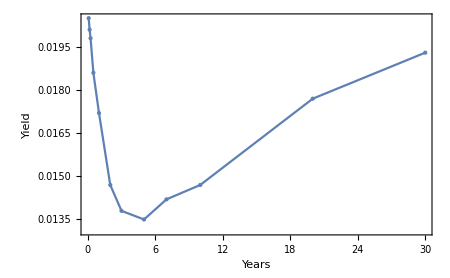

```mathematica
ListLinePlot[mnYieldCurve,
Frame->True,
FrameLabel->{{"Yield",""},{"Years",Column[{Style["US Treasuries",FontSize->16],"{2019, 09, 10}"},Center]}},
PlotStyle->{PointSize[Large]},
Mesh->All,
ImageSize->450
]
```

```mathematica
TableForm[
mnYieldCurve,
TableHeadings->{None,{"Years","Yield"}}
]
```

Years | Yield
1/12 | 0.0205
1/6 | 0.0201
1/4 | 0.0198
1/2 | 0.0186
1 | 0.0172
2 | 0.0147
3 | 0.0138
5 | 0.0135
7 | 0.0142
10 | 0.0147
20 | 0.0177
30 | 0.0193

The US Treasury web site also provides an interactive tool (http://www.treasury.gov/resource-center/data-chart-center/interest-rates/Pages/Historic-Yield-Data-Visualization.aspx) that compares the nominal (i.e., actual) and real (i.e, inflation adjusted) yields for any two dates back to 1990.

#### Example - Spline Interpolation of the Yield Curve

One way of filling in missing periods is to interpolate the yield curve. One of the more effective approaches is to use splines. Interpolation[ ] produces a function based on an interpolation approach selected by the user.

```mathematica
?Interpolation
```

```mathematica
xYieldSpline=Interpolation[mnYieldCurve,Method->"Spline",InterpolationOrder->2]
```

InterpolatingFunction[…]

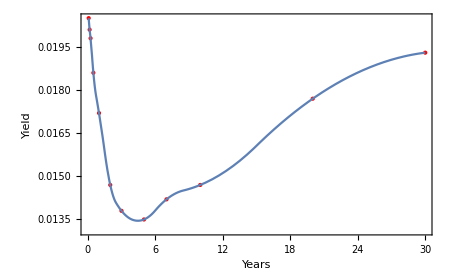

```mathematica
Show[
ListPlot[mnYieldCurve,
Frame->True,
FrameLabel->{{"Yield",""},{"Years",Column[{Style["US Treasuries (Data & 2nd Order Spline)",FontSize->16],"{2019, 09, 10}"},Center]}},
PlotStyle->{Red,PointSize[Large]},
ImageSize->450
],
Plot[xYieldSpline[n],{n,1/12,30},PlotRange->All]
]
```

```mathematica
xYieldSpline[17]
```

0.0167845

```mathematica
xYieldSpline[50]
```

0.0157994

While interpolation produces a useful approximation, using such an approach to extrapolate beyond the range of observed data is dangerous. Sometimes it produces reasonable results but often does not. Also, making the interpolation order higher produces a curve that will match individual observations closely but often can produce ridiculous results.

```mathematica
xYieldSplineBad=Interpolation[mnYieldCurve,Method->"Spline",InterpolationOrder->4]
```

InterpolatingFunction[…]

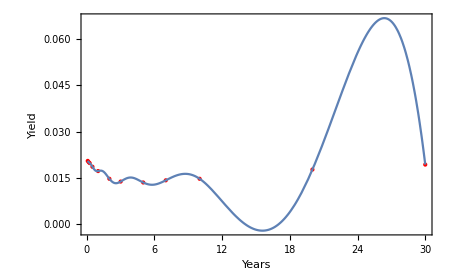

```mathematica
Show[
ListPlot[mnYieldCurve,
Frame->True,
FrameLabel->{{"Yield",""},{"Years",Column[{Style["US Treasuries (Data & 4th Order Spline)",FontSize->16],"{2019, 09, 10}"},Center]}},
PlotStyle->{Red,PointSize[Large]},
ImageSize->450
],
Plot[xYieldSplineBad[n],{n,1/12,30}],
PlotRange->All
]
```

### Spot Rates

The yield on a bond is its overall IRR; however, one implication of the yield curve is that each period has its distinct rate. These rates are called spot rates.

For a zero coupon bond, the yield is the spot rate. In practice, one does not necessarily have bonds at all maturities, so various forms of interpolation must be used to fill in. Also, the spot rates implied by various bonds in the markets may not agree exactly because of differences in supply and demand and some form of averaging must be applied. Nevertheless, the spot rate curve is an important characterization of the time value of money in the market.

In the actual US Treasuries data above, the 1/12-, 1/4-  and 1-year rates are all for bills; hence, the yields shown are already spot rates. The yields for 2 - years and out are nominal yields for notes and bonds that pay semi-annually.

Let S^(n,k), c^(n,k), and F^(n,k) denote the price, coupon and face amount of an n period bond with frequency k and s_i the spot rate of the i^th period (i.e., at time i/k), then the following holds

S^(n,k)=∑_(i=1)^(n×k) c^(n,k)/(1+s_i/k)^i+F^(n,k)/(1+s_(n×k)/k)^(n×k)=∑_(i=1)^(n×k) c^(n,k)/(1+y/k)^i+F^(n,k)/(1+y/k)^(n×k)

### Bootstrapping Spot Rates

For simplicity we’ll illustrate the algebra of bootstrapping the spot rates assuming k=1. For a single period bond, the spot rate is the yield:

S^(1)=F^(1)/(1+y_1)=F^(1)/(1+s_1)

s_1=S^(1)/F^(1)

For a two period bond:

S^(2)=c^(2)/(1+y_2)+(c^(2)+F^(2))/(1+y_2)^2=c^(2)/(1+s_1)+(c^(2)+F^(2))/(1+s_2)^2

and, if we know s_1, then we can solve for s_2:

s_2=((c^(2)+F^(2))/(S^(2)-c^(2)/(1+s_1)))^(1/2)-1

Applying this recursion, if we know s_1, …, s_(n-1), then we can solve for s_n:

s_n=((c^(n)+F^(n))/(S^(n)-∑_(i=1)^(n-1) c^(n)/(1+s_i)^i))^(1/n)-1

Computing spot rates from available market data is simple in principle but difficult in practice. We do not have data at all required maturities and must interpolate. Often market data from other sources, such as various interest rate derivatives, are used to provide a sounder basis for the estimation of the spot rates. Factors such as supply and demand can influence prices in ways that cause unusual perturbations.

For example, on-the-run bonds, bonds that have just been issued, often trade at a slightly higher yield than off-the-run bonds, bonds that were issued some years before. This is due, in part, to the fact that the on-the-run bonds are more in demand. Thus, 20-year bonds 1 year later, effectively a 19-year bond, trade at a yield that not only reflects their 19-year effective term but also the fact they are in less demand than the near equivalent 20-years bonds newly issued. Such factors can introduce kinks in the spot rate curve that are unlikely to reflect economic reality.

### Discount Factors

In certain circumstances it is simpler to view interest rates from the perspective of discount factors. Here d_t represents the discount factor associated with time t.

#### Annual Compounding

d_t≡1/(1+s_t)^t

#### Compounding k Periods/Year

d_t=1/(1+s_t/k)^(k×t)

#### Continuous Compounding

d_t=ⅇ^-s_tt

#### Inner Product Form

Given a vector of discount factors d corresponding to a vector of cash-flow c, the present value of the cash-flows is the inner product of the discount and cash-flow vectors, d^T c.

### Forward Rates

A forward rate is an interest rate agreed to today for money borrowed between two dates in the future. For example, the rate at which money can be borrowed in one year payable back in three years. Consider the forward rate f_(i, j) where i < j. Today you could put $1 in the bank for i periods, then make a forward loan (again making that agreement today) starting at i  for j-i periods. This would be equivalent to loaning it out for j periods today.

(1+s_j)^j=(1+s_i)^i(1+f_(i, j))^(j-i)

If this relationship did not hold, then there would be obvious arbitrage opportunities.

#### Annual Compounding

f_(i, j)=((1+s_j)^j/(1+s_i)^i)^(1/(j-i))-1

#### Compounding k Periods/Year

f_(i, j)=k ((1+s_j/k)^j/(1+s_i/k)^i)^(1/(j-i))-k

#### Continuous Compounding

f_(t_1, t_2)=(t_2 s_2-t_1 s_1)/(t_2-t_1)

### Explanations of the Term Structure

None of the explanations below give a full explanation of the yield or spot rate curve. All, however, probably have some effect.

#### Expectations Theory

The expectation theory (more of a hypothesis) is that the spot rates reflect the market's collective forecast of what rates will be in the future. To some extent this is probably true, but it is unlikely to be a complete explanation. For example, spot rates almost always rise with time, but if the expectations theory were a complete description of the term structure, then that would mean that the market almost always forecasts a rise in rates.

#### Liquidity Preference

The liquidity preference explanation is based on the notion that tying one's capital up for a short-term is better, all else being equal, to tying it up for the long-term. In theory, one can always sell a financial instrument in the market, so a long-term bond isn't necessarily that much more or less liquid than a short-term one, but conditions can arise in which this assumption breaks down. Liquidity offers a partial explanation, but it too cannot be the whole story.

#### Market Segmentation

Market segmentation is a supply-and-demand argument. Different investors have different horizons and the market is broken up into segments, each of which determines its rates independently. This is to some extent true, but investors can construct a debt portfolio any number of ways, blending different instruments at different maturities. While there can be some market segmentation, the notion that the rates are largely determined independently of one another is unlikely to be true.

## Expectation Dynamics

Under expectation dynamics certain consistency relationships hold among yield, spot, forward and short rates. This means that if we have a model for the short rate, then we can use it to produce the entire term structure in all its various forms.

### Spot Rate Forecasts

Let (ŝ)_1, (ŝ)_2, …, (ŝ)_(n-1) denote the forecast of next year's spot rate curve, then clearly

(ŝ)_(j-1)=f_(1, j)=((1+s_j)^j/(1+s_1))^(1/{j-1))-1

### Discount Factors

For a < i < b we have

d_(a, b)=(1/(1+f_(a, b)))^(b-a)

and

d_(a b)=d_(a, i)d_(i, b)

### Short Rates

(1+s_n)^n=(1+r_1)(1+r_2)…(1+r_(n-1))(1+r_n)

(1+s_1)^1=(1+r_1)

(1+s_2)^2=(1+r_1)(1+r_2)

(1+s_n)^n=(1+s_(n-1))^(n-1)(1+r_n)

### The Invariance Theorem

If interest rates evolve according to expectations dynamics, then (under an annual compounding convention) a sum of money invested for n years will grow by a factor of (1+s_n)^n independent of how the funds are invested or reinvested as long as they remain fully invested.

## Capital Budgeting Across Projects

Budgeting for available opportunities given available capital is an important application of optimization.

Evaluating such opportunities involves the computation of net PVs based on the cash flow associated with each opportunity.

### Independent Projects

If we are dealing with independent projects whose benefits (usually PV) are represented by a vector b and costs by a vector c, then, given the total available capital k, we have the zero-one programming problem

max_x { b^T x | c^T x ≤ k, x_i ϵ  {0, 1}}

where x represents a vector of zeroes and ones in which 1 indicates that a project is selected and 0 that it is not.

A common heuristic is to sort the projects by their benefit/cost ratio, and then first pick those projects with highest ratios without violating the total capital constraint.

#### Example — Heuristic Solution

Consider the projects below with the costs and benefits indicated and a total capital budget of 500. The projects are already sorted by their ratios.

```mathematica
vnCosts={100,20,150,50,50,150,150};
vnBenefits={300,50,350,110,100,250,200};
nCapital=500;
```

```mathematica
TableForm[
{vnCosts,vnBenefits,N[vnBenefits/vnCosts]}ᵀ,
TableHeadings->{Automatic,{"Costs","Benefits","Benefit/Cost Ratio"}}
]
```

| Costs | Benefits | Benefit/Cost Ratio
1 | 100 | 300 | 3.
2 | 20 | 50 | 2.5
3 | 150 | 350 | 2.33333
4 | 50 | 110 | 2.2
5 | 50 | 100 | 2.
6 | 150 | 250 | 1.66667
7 | 150 | 200 | 1.33333

Applying the heuristic is simple and produces the following result:

```mathematica
Accumulate[vnCosts]
```

{100,120,270,320,370,520,670}

```mathematica
viHeuristicSolution=If[#≤nCapital,1,0]&/@Accumulate[vnCosts]
```

{1,1,1,1,1,0,0}

```mathematica
vnCosts.viHeuristicSolution
```

370

```mathematica
(vnBenefits-vnCosts).viHeuristicSolution
```

540

The heuristic solution yields an allocation of 370 with a net PV of 540.  Important: The code above only works because the projects are already sorted from highest to lowest by benefit/cost ratio.

#### Example — Integer Linear Programming Solution

First we define a vector of symbols representing the decision variables, one for each project choice:

```mathematica
vxChoices={x1,x2,x3,x4,x5,x6,x7}
```

{x1,x2,x3,x4,x5,x6,x7}

The objective function, as a symbolic expression, is then the inner product the benefits and decision variables:

```mathematica
xObj=(vnBenefits-vnCosts).vxChoices
```

200 x1+30 x2+200 x3+60 x4+50 x5+100 x6+50 x7

We must set the total capital constraint and also constrain each project’s decision variable to be ∈ {0,1}. The latter is done with two constraints: (0≤x_i≤1∧x_i∈ℤ):

```mathematica
vnCosts.vxChoices≤500
```

100 x1+20 x2+150 x3+50 x4+50 x5+150 x6+150 x7≤500

```mathematica
0≤#≤1&/@vxChoices
```

{0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1}

The element-of symbol “∈” is entered as “EscelEsc”:

```mathematica
#∈Integers&/@vxChoices
```

{x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ}

We next Join[ ] the constraints into a single vector …

```mathematica
Join[
{vnCosts.vxChoices≤500},
0≤#≤1&/@vxChoices,
#∈Integers&/@vxChoices
]
```

{100 x1+20 x2+150 x3+50 x4+50 x5+150 x6+150 x7≤500,0≤x1≤1,0≤x2≤1,0≤x3≤1,0≤x4≤1,0≤x5≤1,0≤x6≤1,0≤x7≤1,x1∈ℤ,x2∈ℤ,x3∈ℤ,x4∈ℤ,x5∈ℤ,x6∈ℤ,x7∈ℤ}

… then combine them into a single logical conjunction

```mathematica
xCons=And@@
Join[
{vnCosts.vxChoices≤500},
0≤#≤1&/@vxChoices,
#∈Integers&/@vxChoices
]
```

100 x1+20 x2+150 x3+50 x4+50 x5+150 x6+150 x7≤500&&0≤x1≤1&&0≤x2≤1&&0≤x3≤1&&0≤x4≤1&&0≤x5≤1&&0≤x6≤1&&0≤x7≤1&&x1∈ℤ&&x2∈ℤ&&x3∈ℤ&&x4∈ℤ&&x5∈ℤ&&x6∈ℤ&&x7∈ℤ

The function Maximize[ ] is one of several optimization routines available within Mathematica:

```mathematica
?Maximize
```

```mathematica
Maximize[{xObj,xCons},vxChoices]
```

{610,{x1→1,x2→0,x3→1,x4→1,x5→1,x6→1,x7→0}}

```mathematica
vxChoices
```

{x1,x2,x3,x4,x5,x6,x7}

```mathematica
viOptimalSolution=vxChoices/.Last[Maximize[{xObj,xCons},vxChoices]]
```

{1,0,1,1,1,1,0}

```mathematica
vnCosts.viOptimalSolution
```

500

The optimal solution allocates the entire 500 and realizes a net PV of 610. We can compare heuristic and optimal solutions in the following table.

```mathematica
TableForm[
{vnCosts,vnBenefits,viHeuristicSolution,viOptimalSolution}ᵀ,
TableHeadings->{vxChoices,{"Costs","Benefits","Heuristic","Optimal"}}
]
```

| Costs | Benefits | Heuristic | Optimal
x1 | 100 | 300 | 1 | 1
x2 | 20 | 50 | 1 | 0
x3 | 150 | 350 | 1 | 1
x4 | 50 | 110 | 1 | 1
x5 | 50 | 100 | 1 | 1
x6 | 150 | 250 | 0 | 1
x7 | 150 | 200 | 0 | 0

### Interdependent Projects

When there are interdependencies between projects the basic optimization above is no longer applicable, although the decision can often be represented by a more general zero-one programming problem.

#### Example - One project cannot proceed without the other.

Consider a situation in which if we want to complete project i, then we must also complete project j. An example might be a bridge, which if built, will require a proposed road also be built to handle increased traffic, but the road may be built for other reasons and does not require the bridge be built.

x_i≤x_j

If x_i=1, then that will force (taken in context with the other constraints) x_j=1, as required; however, if x_j=1, then this imposes no additional restrictions on x_i, which may be either 0 or 1.

#### Example - If one project is selected, then at least one of two other projects must also be selected.

Consider a situation in which one project i requires than at least one, but perhaps both, of two other projects j and/or k must be selected. An example might be the building of a sports stadium. The increased traffic must be handled but that can be accomplished two ways. Those two projects may be worthwhile in their own right, however, and selecting either or both of them imposes no requirement that the stadium be built.

x_i≤x_j+x_k

If x_i=1, then that will force at least one of the other projects to be =1, as required; however, if one or both of the other projects =1, then this imposes no additional restrictions on x_i, which may be either 0 or 1.

### Unrealistic Assumptions and Sensitivity Testing

In actual applications, the ability of the decision maker to borrow means that the hard capital constraint is unrealistic, and it’s a good idea to perform a sensitivity analysis by repeating the analysis at different capital levels.

#### Example

We can use the iterator Table[ ] to explore solutions at varying max capital levels. Each case returns the {max capital, net benefit-cost, solution vector}.

```mathematica
vnSensitivityAnalysis=Table[
xCons=And@@
Join[
{vnCosts.vxChoices≤nCapital},
0≤#≤1&/@vxChoices,
#∈Integers&/@vxChoices
];
vxSolution=Maximize[{xObj,xCons},vxChoices];
viOptimalSolution=vxChoices/.Last[vxSolution];
{nCapital,First[vxSolution],viOptimalSolution,viOptimalSolution},
{nCapital,400,700,20}
]
```

{{400,540,{1,1,1,1,1,0,0},{1,1,1,1,1,0,0}},{420,540,{1,1,1,1,1,0,0},{1,1,1,1,1,0,0}},{440,540,{1,1,1,1,1,0,0},{1,1,1,1,1,0,0}},{460,560,{1,0,1,1,0,1,0},{1,0,1,1,0,1,0}},{480,590,{1,1,1,1,0,1,0},{1,1,1,1,0,1,0}},{500,610,{1,0,1,1,1,1,0},{1,0,1,1,1,1,0}},{520,640,{1,1,1,1,1,1,0},{1,1,1,1,1,1,0}},{540,640,{1,1,1,1,1,1,0},{1,1,1,1,1,1,0}},{560,640,{1,1,1,1,1,1,0},{1,1,1,1,1,1,0}},{580,640,{1,1,1,1,1,1,0},{1,1,1,1,1,1,0}},{600,640,{1,1,1,1,1,1,0},{1,1,1,1,1,1,0}},{620,640,{1,1,1,1,0,1,1},{1,1,1,1,0,1,1}},{640,640,{1,1,1,1,0,1,1},{1,1,1,1,0,1,1}},{660,660,{1,0,1,1,1,1,1},{1,0,1,1,1,1,1}},{680,690,{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}},{700,690,{1,1,1,1,1,1,1},{1,1,1,1,1,1,1}}}

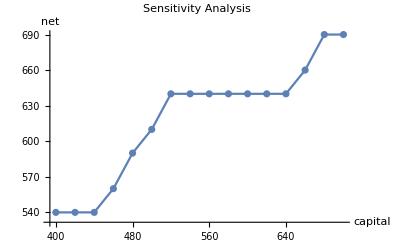

```mathematica
ListPlot[
vnSensitivityAnalysis⟦All,1;;2⟧,
Joined->True,
Mesh->All,
AxesLabel->{"capital","net"},
PlotLabel->Style["Sensitivity Analysis",FontSize->16]
]
```

## Fixed Income Portfolio Optimization

Fixed income instruments can be used to support projects either through borrowing or through investment of current cash in order to ensure that future cash flows will match the funding requirements of those projects in the most cost-effective manner.

### The Cash Matching Problem

The cash matching problem is a common application in which a portfolio of bonds is constructed to meet future cash flow obligations.

The cash matching problem can be formulated as a linear program; specifically, one involving minimizing initial portfolio cost subject to the aggregate cash flow of the bonds meeting those of the obligations.

Let the current prices of available bonds be denoted by the vector p, the cash flow obligations across time by y, and the matrix of bond cash flows by the matrix C in which  c_(i, j) denotes the cash flow from bond j in period i, then we want to

min {p^T x | C x ≥ y, x ≥ 0}

#### Example

```mathematica
vnPrices={109.,94.8,99.5,93.1,97.2,92.9,110.,104.,102.,95.2};
vnCashTargets={100.,200.,800.,100.,800.,1200.};
```

```mathematica
(* c = coupon                     *)
(* f = face amount                *)
(* n = term in payment periods    *)
(* h = horizon in payment periods *)
xBondFlow[c_,f_,n_,h_]:=Join[
Table[c,{i,1,n-1}],
{c+f},
Table[0.,{i,1,h-n}]
];
```

```mathematica
xBondFlow[10,100,3,5]
```

{10,10,110,0.,0.}

```mathematica
xBondFlow[0,100,1,6]
```

{100,0.,0.,0.,0.,0.}

```mathematica
mnCashFlow=Transpose[{
xBondFlow[10,100,6,6],
xBondFlow[7,100,6,6],
xBondFlow[8,100,6,6],
xBondFlow[6,100,5,6],
xBondFlow[7,100,5,6],
xBondFlow[5,100,4,6],
xBondFlow[10,100,3,6],
xBondFlow[8,100,3,6],
xBondFlow[7,100,2,6],
xBondFlow[0,100,1,6]
}];
MatrixForm[mnCashFlow]
```

(10 | 7 | 8 | 6 | 7 | 5 | 10 | 8 | 7 | 100
10 | 7 | 8 | 6 | 7 | 5 | 10 | 8 | 107 | 0.
10 | 7 | 8 | 6 | 7 | 5 | 110 | 108 | 0. | 0.
10 | 7 | 8 | 6 | 7 | 105 | 0. | 0. | 0. | 0.
10 | 7 | 8 | 106 | 107 | 0. | 0. | 0. | 0. | 0.
110 | 107 | 108 | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
?LinearProgramming
```

```mathematica
vnOptimalPortfolio=LinearProgramming[vnPrices,mnCashFlow,vnCashTargets]
```

{0.,11.215,0.,6.80656,0.,0.,0.,6.30237,0.282589,0.}

```mathematica
vnOptimalPortfolio.vnPrices
```

2381.14

```mathematica
Chop[mnCashFlow.vnOptimalPortfolio-vnCashTargets]
```

{71.7411,0,0,19.344,0,0}

### The Cash Matching Problem with Surpluses

Initially as above, we are given C the cash flow matrix, x the vector positions to be determined, and y the vector of obligations. In each period any surplus cash not used for that period's obligations we wish to roll over to make it available for use in the next period. We want to be conservative and so will assume we earn no interest on this surplus cash.

Define s ≥ 0 the vector of cash surpluses available in each period. In the first period the relevant constraint is

C⟦1, All⟧ . x  –  s⟦1⟧ == y⟦1⟧

In the next period, we have the cash flows available from the bonds and the surpluses available from the prior period invested at some constant short-term rate r; otherwise, the constraint is the same:

C⟦2, All⟧ . x +(1+r) s⟦1⟧ – s⟦2⟧ == y⟦2⟧.

And in general for j ∈ {2,⋯, n}

C⟦j, All⟧ . x + (1+r)s⟦j – 1⟧ – s⟦j⟧ == y⟦j⟧.

## Dividend Discount Model

The dividend discount model (http://en.wikipedia.org/wiki/Dividend_discount_model) values a company’s stock by computing the PV of all of its future dividend payments or, alternatively, its future earnings.

Despite its limitations, the dividend discount model can serve as a useful tool by illustrating key assumptions implied by the valuation of a given stock and by providing insight into how changes in those assumptions may influence its price.

The basic form of the dividend discount model is to compute the price of a stock as the PV of its dividends. At t=0, if S_0 is the current price of the stock, D_i is the dividend to be recieved at t=i, and r_i is the return to be used to discount during the interval t=i-1 to i, then

S_0=D_1/(1+r_1)+D_2/((1+r_1)(1+r_2))+⃛

### Constant Discount and Dividend

Let D denote the value of the dividend and assume the return is constant, then:

S_0=D/(1+r)+D/(1+r)^2+⃛=∑_(k =1)^∞ D/(1+r)^k=D/r

```mathematica
FullSimplify[Sum[d/(1+r)^i,{i,1,Infinity}]]
```

d/r

### Constant Discount with Constant Growth

It is often assumed that for various reasons, for example, general economic growth or increasing market share, the dividend will grow over time. If that growth is assumed to be constant at rate g, then with D_1 representing the dividend to be received one period hence:

S_0=D_1/(1+r)+((1+g)D_1)/(1+r)^2+((1+g)^2 D_1)/(1+r)^3+⃛=D_1∑_(k =1)^∞ (1+g)^(k-1)/(1+r)^k=D_1 1/(r-g)

```mathematica
FullSimplify[∑_(k=1)^∞ (1+g)^(k-1)/(1+r)^k]
```

1/(-g+r)

If D_0 is the current dividend just paid, then under the same assumptions D_1=D_0(1+g) and

S_0= D_1 1/(r-g)=D_0(1+g)/(r-g)

In problems it’s important to keep straight whether one is dealing with D_0 or D_1 when dividends are specified.

#### Example - Implied Price

The XYZ corporation has just paid a dividend of $1.37 million and expects to grow at 10% annually for the foreseeable future with corresponding growth in dividends. The discount rate used for this type of company is 15%. What market capitalization is implied under the dividend discount model?

Note that D_0=1.37×10^6 so that the next dividend is D_1=(1+g)D_0.

```mathematica
nGrowthRate=0.1
nDiscountRate=0.15
nNextDividend=(1+nGrowthRate)1.37 10^6
nImpliedValuation=nNextDividend/(nDiscountRate-nGrowthRate)
```

0.1

0.15

1.507×10^6

3.014×10^7

Thus, the value of XYZ is $30,140,000.

#### Example - Implied Growth Rate

The XYZ corporation has just paid a dividend of $1.37 million and has a total market capitalization of $36,500,000. The discount rate used for this type of company is 15%. What is the implied growth rate for the dividends of this stock?

Note that D_0=1.37×10^6 so that the next dividend is D_1=(1+g)D_0.

S_0= D_0(1+g)1/(r-g)   ⟹   g=(r S_0-D_0)/(S_0+D_0)

```mathematica
nDiscountRate=0.15
nCurrentDividend=1.37 10^6
nValuation=36.5 10^6
nImpliedGrowthRate=(nDiscountRate nValuation-nCurrentDividend)/(nValuation+nCurrentDividend)
```

0.15

1.37×10^6

3.65×10^7

0.108397

Thus, the implied growth rate for XYZ consistent with this valuation is 10.84%. We can examine this computation for various market caps with the following plot:

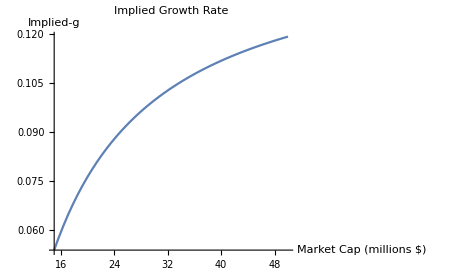

```mathematica
Plot[
(nDiscountRate v 10^6-nCurrentDividend)/(v 10^6+nCurrentDividend),
{v,15,50},
PlotLabel->Style["Implied Growth Rate",FontSize->14],
AxesLabel->{"Market Cap (millions $)","Implied-g"},
ImageSize->450
]
```

### Free Cash Flow

Free cash flow is the cash generated through operations less the investments necessary to sustain those operations and their future growth. It is difficult to measure but probably represents a better measure of the value of continuing operations to an investor than do dividends.

#### Example

The new internet company Bamboozel has a projected free-cash flow of $1,250,000 per year. An appropriate discount rate for a company of this type appears to be 10%. The current market value of Bamboozel's shares is $73,500,000. What is the implied growth rate in free cash flow under the constant discount, constant growth assumption?

We employ the following formula with D_1 now representing the projected free cash flow rather than the projected dividend:

S_0=D_1 1/(r-g)

We’ll take this as an opportunity to illustrate the use of Mathematica’s FindRoot[ ]:

```mathematica
nDiscountRate=0.10
nFreeCashFlow=1.25 10^6
nMarketCap=73.5 10^6
FindRoot[nMarketCap==nFreeCashFlow/(nDiscountRate-g),{g,nDiscountRate/2}]
```

0.1

1.25×10^6

7.35×10^7

{g→0.0829932}

The implied growth rate is 8.3%.

The market value drops to $65,000,000 over concerns about competitive pressures. The implied growth rate

```mathematica
Solve[c==f/(r-g),g]
```

{{g→(-f+c r)/c}}

```mathematica
nMarketCap=65 10^6
Solve[nMarketCap==nFreeCashFlow/(nDiscountRate-g),g]
```

65000000

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{g→0.0807692}}

drops from 8.3% to 8.1%.

Later in the year the market rallies and the values of the company's shares rises to $105,000,000. The implied growth rate

```mathematica
nMarketCap=105 10^6
FindRoot[nMarketCap==nFreeCashFlow/(nDiscountRate-g),{g,0.08}]
```

105000000

{g→0.0880952}

For growth stocks, i.e., stocks whose valuation is predicated on expectations of high growth, changes in economic expectations can have an enormous effect on valuation. Consider a more general case in which we solve for market capitalization as a function of growth. Consider the following:

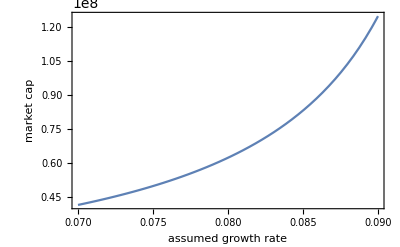

```mathematica
Plot[
nFreeCashFlow/(nDiscountRate-g),
{g,0.07,0.09},
Frame->True,
FrameLabel->{"assumed growth rate","market cap",Style["Price Analysis",FontSize->14],""},
Axes->False
]
```

Note that what would seem like a modest reduction in expected growth of from 9% to 7% results in the value of Bamboozel being cut by two-thirds! This effect explains, to some degree, the collapse of the Tech Bubble at the turn of the century. Investors were buying stock with no earnings based on extremely optimistic assumptions of future growth. When it became obvious that those future earnings were not likely to materialize, the market crashed.

### Multi-Stage Model

#### Two-Stage Model

One criticism of the dividend discount model is that it contains a fixed growth rate. A more realistic model for a young, high-growth company is that its growth will eventually mature to a more “normal” level. The two-stage dividend discount model has an initial, typically high, growth rate g that will hold until the end of period n, after which it transitions to a long-term growth level γ. Normally, g>γ. The model, therefore, is:

S_0=D_1(∑_(i=1)^n (1+g)^(i-1)/(1+r)^i+∑_(i=n+1)^∞ (1+γ)^(i-1)/(1+r)^i)

We’ll analyze the two summations above separately, color coding them green and magenta:

∑_(i=1)^n (1+g)^(i-1)/(1+r)^i+∑_(i=n+1)^∞ (1+γ)^(i-1)/(1+r)^i

First, we’ll analyze the first (green) summation above. Note that we can represent it as the difference between two summations as below. One (red) that is the familiar dividend discount model already solved and another (blue) that takes out the periods from n+1 onwards:

∑_(i=1)^n (1+g)^(i-1)/(1+r)^i=∑_(i=1)^∞ (1+g)^(i-1)/(1+r)^i-∑_(i=n+1)^∞ (1+g)^(i-1)/(1+r)^i

The solution of the former (red) has already been worked out:

∑_(i=1)^∞ (1+g)^(i-1)/(1+r)^i=1/(r-g)

For the latter (blue) we can factor our a ((1+g)/(1+r))^n term, translating translating it back to i=1, yielding:

∑_(i=n+1)^∞ (1+g)^(i-1)/(1+r)^i=((1+g)/(1+r))^n∑_(i=0)^∞ (1+g)^(i-1)/(1+r)^i=((1+g)/(1+r))^n 1/(r-g)

Combining our results so far gives us the solution the first (green) summation in the two-stage dividend discount model:

∑_(i=1)^n (1+g)^(i-1)/(1+r)^i=1/(r-g)-((1+g)/(1+r))^n 1/(r-g)

We can simplify further to produce our partial solution covering the first (green) summation:

∑_(i=1)^n (1+g)^(i-1)/(1+r)^i=1/(r-g)(1-((1+g)/(1+r))^n)

```mathematica
FullSimplify[∑_(i=1)^n (1+g)^(i-1)/(1+r)^i]
```

-(1-(1+g)^n (1+r)^-n)/(g-r)

For the second (magenta) summation shown in the first equation above we can repeat the technique of factoring out a ((1+γ)/(1+r))^n term, translating the remaining summation back to i=1, yielding:

∑_(i=n+1)^∞ (1+γ)^(i-1)/(1+r)^i=1/(r-γ)((1+γ)/(1+r))^n

```mathematica
FullSimplify[∑_(i=n+1)^∞ (1+γ)^(i-1)/(1+r)^i]
```

((1+r)^-n (1+γ)^n)/(r-γ)

Combining these partial solutions together gives us our closed-form solution for the two-stage dividend discount model:

S_0=D_1(1/(r-g)(1-((1+g)/(1+r))^n)+1/(r-γ)((1+γ)/(1+r))^n)

where, as before, D_1=(1+g)D_0.

#### Mathematica Function

Implementing the above as a Mathematica function involves little more than transcribing the equation:

```mathematica
xTwoStageDDM[d1_,r_,g_,n_,γ_]:=d1(1/(r-g)(1-((1+g)/(1+r))^n)+1/(r-γ)((1+γ)/(1+r))^n);
```

#### Example - Two-Stage Model

SoundDazzler just issued an annual dividend of $5/share. It is a tech firm that has been growing at more than 20% per year, a rate that you believe can continue 5 more years before settling into a long-run rate of 3% per year. A suitable rate for discounting this stock is 12%. Given these assumptions, what is a suitable share price for SoundDazzler?

```mathematica
xTwoStageDDM[1.2 5,0.12,0.20,5,0.03]
```

74.749

Thus, a price of $74.75 per share is consistent with those assumptions. Note that the problem specified D_0 and we must compute D_1=(1+g)D_0 which is the argument the function is expecting.

Also, note that growth companies often do not declare dividends, instead reinvesting their earnings to fund future expansion. In such instances a measure such as free cash flow would be used instead of dividends paid.

It is simple enough to do a sensitivity analysis, illustrating how S changes with n and g. We’ve placed a red point at the solution point above:

```mathematica
Show[
Plot3D[xTwoStageDDM[(1+g) 5,0.12,g,n,0.03],{n,3,7},{g,0.15,0.25},AxesLabel->{"n","g","S"}],
Graphics3D[{Red,PointSize[0.02],Point[{5,0.20,xTwoStageDDM[1.2 5,0.12,0.20,5,0.03]}]}]
]
```

-Graphics3D-

#### Multi-Stage Models

Obviously, the abrupt transition in the two-stage model, while perhaps better than the fixed growth rate of the original, can be made more representative by using a more complex growth model. The discount rate can also be subject to the same kind of adjustment.

One might have different growth rates at different stages of the company’s life-cycle (see for example http://en.wikipedia.org/wiki/Organizational_life_cycle) and have the current discount rate gradually return to a long-term mean rate. Care must be taken in making models overly complex without a solid foundation. Adding a lot of parameters can give you a model that will say nothing because it can say anything. It will be calibrated it to mirror one’s own biases or be over-fit to the data.

Clearly, there are a number of models possible within this framework, e.g., allowing for a period of losses before profitability is achieved.

#### A Serious Concern

Perhaps the most serious concern about the dividend discount model is that it treats the dividend stream and the rates used to calculate that stream’s present value as completely deterministic, a quite unreasonable assumption. Thus, sensitivity analysis is important. Nevertheless, the dividend discount model can provide useful insights especially in comparing the valuations of different stocks and in examining the nonlinear effects of our assumptions. The model can also be extended to a Monte Carlo simulation where these key assumptions are treated as random variables.

## FinancialBond[ ]

The FinancialBond[ ] function is another built-in Mathematica financial function which supports computations associated with bonds. These computations include pricing, accrued interest, and yield calculations under a variety of date and calendar conventions.

FinancialBond[ ] is a Mathematica object that gives the value and other properties of a bond. Using it effectively, however, demands that you understand the computations it performs. It provides a powerful tool for the valuation of fixed income instruments, including pricing after issuance, different calendar conventions, and the computation of additional measures such as accrued interest.

```mathematica
?FinancialBond
```

#### Pricing at Issuance

Issue price of a 30-year semi-annual bond with face value $10,000, nominal interest rate of 10% with a 6% yield:

```mathematica
FinancialBond[{"Coupon"->0.10,"FaceValue"->10000,"Maturity"->30,"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->0}]
```

15535.1

Here is an alternate PV computation using TimeValue[ ], Annuity[ ], and EffectiveInterest[ ]; note that the payments specified in Annuity[ ] includes extra terms which specify additional amounts added to the initial and final payments of the stream.

```mathematica
TimeValue[Annuity[{0.10/2 10000,{0,10000}},30,1/2],EffectiveInterest[0.06,1/2],0]
```

15535.1

#### Pricing after Issuance (two examples: relative time and actual date)

Price of a 10-year semiannual coupon bond with a coupon rate of 5.75% and a 5% yield 9 months after the issue date:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.0575,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->.05,"Settlement"->9/12}]
```

1054.92

Price of a 4% coupon quarterly bond maturing December 31, 2030 and settling October 28, 2019 assuming the yield is at par:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.04,"Maturity"->{2030,12,31},"CouponInterval"->1/4},{"InterestRate"->.04,"Settlement"->{2019,10,28}}]
```

999.989

… assuming the yield is at 6%, and, hence, the bond is at discount:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.04,"Maturity"->{2030,12,31},"CouponInterval"->1/4},{"InterestRate"->.06,"Settlement"->{2019,10,28}}]
```

837.997

… assuming the yield is at 3%, and, hence, the bond is at premium:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.04,"Maturity"->{2030,12,31},"CouponInterval"->1/4},{"InterestRate"->.03,"Settlement"->{2019,10,28}}]
```

1094.63

#### Accrued Interest

Accrued interest for a semiannual bond maturing on December 31, 2030 and settling on November 12, 2020, using the Actual/360 day count convention:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.07,"Maturity"->{2030,12,31},"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->{2020,11,12},"DayCountBasis"->"Actual/360"},"AccruedInterest"]
```

26.25

... using the 30/360 convention:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.07,"Maturity"->{2030,12,31},"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->{2019,11,12},"DayCountBasis"->"30/360"},"AccruedInterest"]
```

25.6667

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.07,"Maturity"->{2030,12,31},"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->{2019,11,12}},"AccruedInterest"]
```

25.6793

#### Yield Computation (using FindRoot[ ])

Implied yield to maturity for a quarterly coupon bond valued at $900:

```mathematica
nYieldExample=y/.FindRoot[FinancialBond[{"FaceValue"->1000,"Coupon"->0.05,"Maturity"->{2028,6,30},"CouponInterval"->1/4},{"InterestRate"->y,"Settlement"->{2020,1,6}}]==900,{y,.05}]
```

0.0654544

#### Yield versus Price Analysis (Using Table[ ], TableForm[ ], and ListLinePlot[ ])

```mathematica
mnYieldVsPrice=Table[
{
p,
y/.FindRoot[
FinancialBond[
{"FaceValue"->1000,"Coupon"->0.05,"Maturity"->{2028,6,31},"CouponInterval"->1/4},
{"InterestRate"->y,"Settlement"->{2020,1,6}}
]==p,
{y,0.05/2 1000}
]
},
{p,750,1250,50}
]
```

{{750,0.0929056},{800,0.0830763},{850,0.0739555},{900,0.0654506},{950,0.0574861},{1000,0.0499994},{1050,0.0429379},{1100,0.0362573},{1150,0.0299196},{1200,0.0238923},{1250,0.0181472}}

```mathematica
TableForm[mnYieldVsPrice,TableHeadings->{None,{"Price","Yield"}}]
```

Price | Yield
750 | 0.0929056
800 | 0.0830763
850 | 0.0739555
900 | 0.0654506
950 | 0.0574861
1000 | 0.0499994
1050 | 0.0429379
1100 | 0.0362573
1150 | 0.0299196
1200 | 0.0238923
1250 | 0.0181472

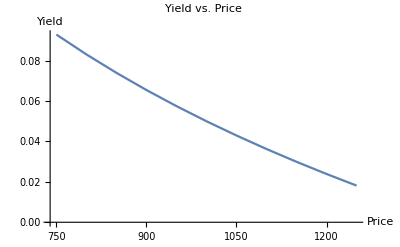

```mathematica
ListLinePlot[mnYieldVsPrice,AxesLabel->{"Price","Yield"},PlotLabel->Style["Yield vs. Price",FontSize->14]]
```